```mathematica
Raumtemperatur IQE Bestimmung
```

## Konstante Koeffzienten

```mathematica
a0GaN= Quantity[2×10^5,"Centimeter^(-1)"];
a0AlN= Quantity[1×10^5,"Centimeter^(-1)"];
E0=Quantity[6.424,"eV"];
AlN=Quantity[6.28, "eV"];
GaN=Quantity[3.44, "eV"];
AlContent:= 0.72;
a0= a0AlN *AlContent+ a0GaN*(1-AlContent);
EG=AlN×(AlContent)+GaN(1-AlContent);
```

## Grafische Darstellung

{{4320.56,598.73},{4008.16,549.362},{2799.56,393.475},{2629.31,331.002},{2221.67,317.311},{2029.26,260.853},{1822.42,234.694},{1647.98,216.444},{1567.33,214.978},{1408.,193.43},{1062.8,131.846},{969.07,120.304},{1155.76,148.561},{1060.62,131.934},{627.39,79.29},{575.95,70.5804},{402.2,50.0025},{377.9,42.0675},{315.78,37.7509},{294.72,34.3249},{263.53,30.5923},{266.77,29.5757},{247.48,26.3023},{172.86,18.2627},{162.34,14.8172},{137.18,13.0259},{125.29,10.7336},{112.53,9.69096},{101.76,8.10465},{96.77,7.723},{86.93,6.84664},{65.62,4.26103},{59.83,3.71034},{71.36,4.81381},{65.5,4.21061},{38.75,2.38361},{35.57,2.16025},{24.83,1.50021},{23.33,1.2022},{19.5,1.07409},{16.28,0.875288},{11.49,0.538747},{10.65,0.470909},{7.44,0.330023},{6.99,0.277862},{5.91,0.244719},{5.4,0.208622},{4.85,0.189478},{4.38,0.162302},{4.18,0.160538},{3.75,0.174405},{2.83,0.0950511},{2.59,0.0953516},{3.08,0.0930251},{2.81,0.0854718},{1.67,0.0563263},{1.53,0.0422356},{1.08,0.0275608},{1.,0.0196592},{0.84,0.0140827},{0.69,0.0145672}}

```mathematica
mmm=N[Import["C:\\Users\\studi\\Documents\\TS3931 swap.txt","Table"]];
exPOWden = mmm[[;;,1]] ;
int = mmm[[;;,2]] ;
name1 = InputString[];
mmm = Transpose[{int,exPOWden}];
(*
ListPlot[mmm,PlotLegends->name1,ImageSize->400,PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Excitation power density",20]},PlotTheme->"Detailed"]
*)
```

```mathematica
mm1 =ArrayReshape[mmm,{61,2}] ;
ll=mm1[[All,1]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21 ;
öö = mm1[[All,2]];
sort1 = Sort[Transpose[{öö,ll}]];
Manipulate[Row[{ListPlot[sort1[[ii ;; i]]  /.x-> α  /.r->R,PlotRange-> Full, PlotLegends->{name1},
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},ImageSize-> 400,
PlotTheme->"Detailed"],ListLogLogPlot[N[sort1[[ii ;; i]]]  /.x-> α  /.r->R,PlotRange-> Full, PlotLegends->{name1},ImageSize->400,
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},
PlotTheme->"Detailed"]}],{α, 1*10^4, 1*10^8},{R, 0.1,1.0},{{i,39,"Anzahl Messdaten bis"},1,39,1},{{ii ,20,"Anzahl Messdaten von"},1,39,1}]
```

```mathematica
Module[{x=1*10^5, r:=0.44},
Manipulate[par1 = FindFit[sort1[[n ;; m]],z1*√y+ z2 * y,{z1,z2},y];
a111=(z1/.par1[[1]]);
a222=(z2/.par1[[2]]);
Show[ListPlot[sort1[[n ;; m]],PlotLegends->{},PlotTheme-> "Detailed",ImageSize->400],Plot[{  a111*√p+a222*p },{p,0,6000},PlotRange->Automatic]] ,{{n,1,"Anzahl Messdaten bis"},1,39,1},{{m,39,"Anzahl Messdaten von"},39,60,1}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

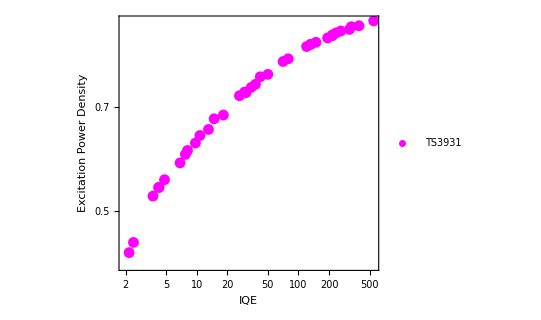

```mathematica
par5[ai_,bi_]:=FindFit[sort1[[ai ;; bi]],z1*√y+ z2 * y,{z1,z2},y]
ai = 25;
bi = 60;
eins = par5[ai,bi];
a111=(z1/.eins[[1]]);
a222=(z2/.eins[[2]]);
Erg1=Solve[a111/√a222*B1 + B1^2 == sort1[[n,2]],B1];
Ergebnisse =Table[Erg1,{n,ai,bi,1}];

anm=B1/.Ergebnisse[[;;,2]];
IQE1Tab = (anm[[;;]]^2)/(sort1[[ai;; bi,2]]);
snew=Sort[s[[;;,2]]];
snew1= snew[[ai;;bi]];
t11=Transpose[{snew1,IQE1Tab}];
ListLogLogPlot[t11,PlotLegends->Placed[{TS3931 },{0.85,0.25}],PlotStyle->{Black, Red,Blue, Magenta},PlotRange->Full, PlotTheme->"Detailed",AspectRatio-> 0.8/1,AxesLabel->{"IQE","Excitation Power Density"}]
```

```mathematica
Manipulate[par5[ai_,bi_]=FindFit[sort1[[ai ;; bi]],z1*√y+ z2 * y,{z1,z2},y];
eins = par5[ai,bi];
a111=(z1/.eins[[1]]);
a222=(z2/.eins[[2]]);
Erg1=Quiet@Solve[a111/√a222*B1 + B1^2 == sort1[[n,2]],B1];
Ergebnisse =Table[Erg1,{n,ai,bi,1}];

anm=B1/.Ergebnisse[[;;,2]];
IQE1Tab = (anm[[;;]]^2)/(sort1[[ai;; bi,2]]);
snew=Sort[s[[;;,2]]];
snew1= snew[[ai;;bi]];
t11=Transpose[{snew1,IQE1Tab}];
ListPlot[t11,PlotLegends->Placed[{TS3931 },{0.85,0.25}],PlotRange->Full, PlotTheme->"Detailed",AspectRatio-> 0.8/1,AxesLabel->{"IQE","Excitation Power Density"}],{{ai,1,"Anzahl Messdaten bis"},1,39,1},{{bi,39,"Anzahl Messdaten von"},39,60,1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.